```mathematica
ClearAll["Global`*"]
```

# Defining Domain and Mesh for Cerebral Aneurism

## Inputs

We difine our geometry in terms of ℛs for length units, ℛ := radius of the vessel, meters.

```mathematica
ℒ=16;(* length of the vessel *)
𝒟=4;(* diameter of the aneurysm *)
𝒩=3;(* length of the aneurism’s “neck” *)
```

## Analytic Domain Ω

```mathematica
vessel=Rectangle[{-ℒ/2,-1},{ℒ/2,1}];
aneurysm=Disk[{0,1+𝒟/2},𝒟/2];
```

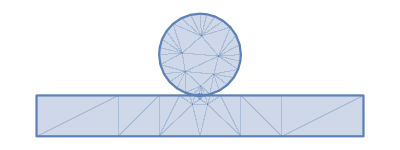

```mathematica
RegionPlot[RegionUnion[vessel,aneurysm],AspectRatio->Automatic,Frame->None]
```

```mathematica
𝓇=𝒩^2/(8 𝒟);
neck=RegionDifference[
RegionUnion[
Rectangle[{-𝒩/2,0},{𝒩/2,1+𝓇}],
Triangle[{{𝒩/2,1+𝓇},{0,1+𝒟/2},{-𝒩/2,1+𝓇}}]
],
RegionUnion[
Disk[{𝒩/2,1+𝓇},𝓇],
Disk[{-𝒩/2,1+𝓇},𝓇]
]];
```

```mathematica
Ω=RegionUnion[vessel,neck,aneurysm];
```

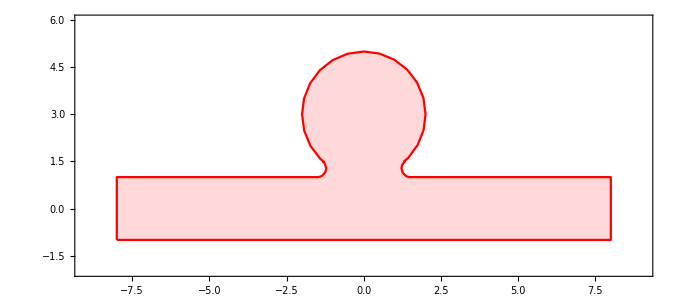

```mathematica
RegionPlot[Ω,AspectRatio->Automatic,
PlotStyle->LightRed,BoundaryStyle->Red,
PlotRange->{{-ℒ/2-1,ℒ/2+1},{-2,2+𝒟}},
Axes->True
]
```

## Mesh 𝒯

```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
NotebookEvaluate[dir<>"../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.5,.5];
```

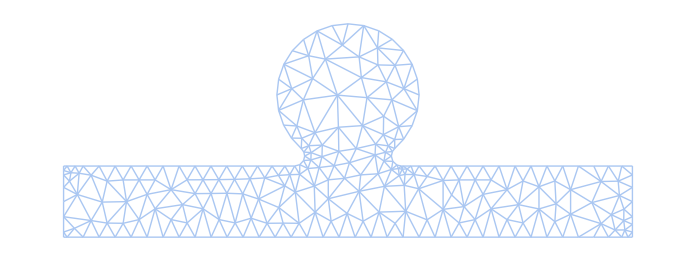

```mathematica
highlight[𝒯,{},0]
```